```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes CAN

tmp

## temp

### Definition / Theorem

#### Example

Complex Integration

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
path[n_]:= Table[Exp[2*I*Pi*k/n], {k, 0, n}]

PlotPath[path_ , options___] :=
Module[{argand = Map[{Re[#], Im[#]}&, path]},grdata = {Line[argand],{PointSize[0.03],  Map[Point, argand]}};
Show[Graphics[grdata,AspectRatio -> 1,  Axes -> True, options]]]
```

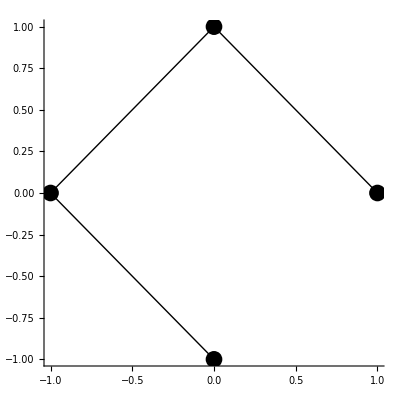

```mathematica
psp = {1, I, -1, -I};PlotPath[psp]
```

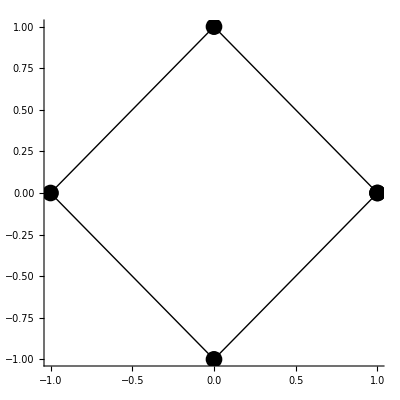

```mathematica
cpsp = {1, I, -1, -I, 1};PlotPath[cpsp]
```

```mathematica
ContourIntegral[expr_, vbl_, contour_] :=
	Integrate[expr, Prepend[contour, vbl]]
```

```mathematica
NContourIntegral[expr_, vbl_, contour_] :=
	NIntegrate[expr,Evaluate[ Prepend[contour, vbl]]]
```

```mathematica
ContourIntegral[1/z,z,cpsp]//Chop
```

2 ⅈ π

```mathematica
ContourIntegral[Sin[z]/z^2,z,cpsp]//Chop
```

2 ⅈ π

```mathematica
ContourIntegral[ⅇ^(-π z),z,{-ⅈ,ⅈ}]
```

0

```mathematica
ContourIntegral[(3z-1)^4,z,{2,2I+1/3 }]
```

-625/3+(2592 ⅈ)/5

```mathematica
ContourIntegral[z^2,z,{0,1+I}]//Expand
```

-2/3+(2 ⅈ)/3

```mathematica
ContourIntegral[1/z,z,-3/4-2/4I+path[12]]//Expand
```

2 ⅈ π

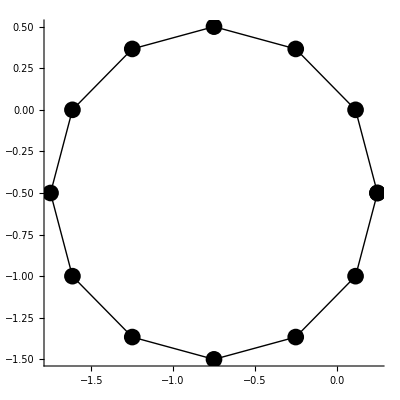

```mathematica
PlotPath[-3/4-2/4I+path[12]]
```

```mathematica
ClearAll[a,f,g]
f[z_]:=1/z
f[z_]:=Conjugate[z]
g[t_]:=ⅇ^(2π ⅈ t)
Integrate[f[g[t]]g'[t],{t,0,1},Assumptions->{Re[a]>1}]
```

2 ⅈ π

```mathematica
ContourIntegral[Conjugate[z],z,path[6]]//Expand
```

3 ⅈ √3